# PieChart - Sample of countries

```mathematica
(*Quit*)
```

## 2016

```mathematica
SetDirectory[$UserDocumentsDirectory]
```

/home/drigo/Documents

```mathematica
Get["datasets2016.mx"]
```

```mathematica
Get["aGENCY2016.mx"]
```

```mathematica
Get["categorieS2016.mx"]
```

```mathematica
aGENCY2016
```

{Overseas Private Investment Corporation,Department of Defense,Peace Corps,U.S. Agency for International Development,U.S. Department of State,U.S. Department of the Treasury,Inter-American Foundation,Department of Interior,U.S. African Development Foundation,Department of Justice,Department of Labor,U.S. Department of Agriculture}

```mathematica
Length[aGENCY2016]
```

12

```mathematica
categorieS2016
```

{Economic Development,Peace and Security,Program Management,Multi-sector,Education and Social Services,Democracy, Human Rights, and Governance,Humanitarian Assistance,Health,Environment}

```mathematica
Length[categorieS2016]
```

9

```mathematica
dataAlltogether2016=Flatten@Values[datasetsCS2016];
```

```mathematica
coutr2016=DeleteDuplicates[Table[dataAlltogether2016[[i]][["BenefitingLocation"]],{i,1,Length[dataAlltogether2016]}]]
```

{Jordan,Algeria,Angola,Argentina,Armenia,China,Croatia,Estonia,Ethiopia,Georgia,Kenya,Latvia,Libya,Namibia,Russia,Somalia,Uganda,Bulgaria,Liberia,Slovakia,Chile,Portugal,Israel,Nigeria,Niger,Venezuela,Cuba,Ecuador,Guatemala,Honduras,Mexico,Peru,Afghanistan,Albania,Azerbaijan,Bahamas, The,Bahrain,Bangladesh,Barbados,Belarus,Belize,Benin,Bolivia,Botswana,Brazil,Brunei,Burundi,Cambodia,Cameroon,Canada,Chad,Colombia,Comoros,Cyprus,Djibouti,Dominican Republic,Egypt,Eritrea,Fiji,Gabon,Gambia, The,Ghana,Greece,Grenada,Guinea,Guinea-Bissau,Equatorial Guinea,Papua New Guinea,Guyana,Haiti,Hungary,India,Indonesia,Iran,Iraq,Jamaica,Japan,Kazakhstan,Kosovo,Kuwait,Kyrgyzstan,Laos,Lebanon,Lesotho,Lithuania,Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Mauritania,Mauritius,Micronesia, Federated States of,Moldova,Mongolia,Montenegro,Morocco,Mozambique,Nepal,Nicaragua,Oman,Romania,Pakistan,Palau,Panama,Paraguay,Philippines,Poland,Qatar,Rwanda,Samoa,Senegal,Serbia,Seychelles,Spain,South Sudan,Sudan,Swaziland,Syria,Tajikistan,Tanzania,Thailand,Togo,Tonga,Tunisia,Turkey,Turkmenistan,Ukraine,Uruguay,Uzbekistan,Vanuatu,Vietnam,Yemen,Zambia,Zimbabwe}

```mathematica
Length[coutr2016]
```

136

```mathematica
AnalysisGivenCountry2016[country_,category_]:=With[{r=Select[Select[dataAlltogether2016,#[[5]]==country&],#[[3]]==category&]},If[Length[r]==0,{Association[Rule["AgencyName",""],Rule["Amount","0.00"],Rule["Category",""],Rule["Year",""],Rule["BenefitingLocation",country],Rule["Sector",""]]},r]];
```

```mathematica
DollarIssue2016[country_,category_]:=MapAt[Interpreter[Restricted["StructuredQuantity","USDollars"]],AnalysisGivenCountry2016[country,category],{1;;,2}];
```

```mathematica
DollarIssueOnhe02016[country_,category_]:=Cases[DollarIssue2016[country,category],HoldPattern[<|_String->_String,_String-> Quantity[x_/;x>0,"USDollars"],_String->_String,_String->_String,_String->_String,_String->_String|>]]
```

```mathematica
total2016[country_]:=Association[Map[#->Total[Table[DollarIssueOnhe02016[country,#][[i]]["Amount"],{i,1,Length[DollarIssueOnhe02016[country,#]]}]]&,categorieS2016]]
```

```mathematica
totalpiechartCountry2016[country_]:=Total[Values[total2016[country]]]
```

```mathematica
ModpiechartPais2016[country_]:=PieChart[total2016[country],ChartLegends->Keys[total2016[country]],PlotLabel->country (Total[Values[total2016[country]]])]
```

```mathematica
peru2016=ModpiechartPais2016["Peru"]
```

-Graphics-

```mathematica
jordan2016=ModpiechartPais2016["Jordan"]
```

-Graphics-

```mathematica
chile2016=ModpiechartPais2016["Chile"]
```

-Graphics-

```mathematica
ethiopia2016=ModpiechartPais2016["Ethiopia"]
```

-Graphics-

## 2015

```mathematica
Get["datasets2015.mx"]
```

```mathematica
Get["aGENCY2015.mx"]
```

```mathematica
Get["categorieS2015.mx"]
```

```mathematica
aGENCY2015
```

{U.S. Department of State,Millennium Challenge Corporation,Department of Health and Human Services,U.S. Agency for International Development,Department of Defense,Overseas Private Investment Corporation,U.S. Department of Agriculture,Peace Corps,U.S. Department of the Treasury,Inter-American Foundation,Department of Interior,Department of Labor,U.S. African Development Foundation,Department of Justice}

```mathematica
Length[aGENCY2015]
```

14

```mathematica
categorieS2016
```

{Economic Development,Peace and Security,Program Management,Multi-sector,Education and Social Services,Democracy, Human Rights, and Governance,Humanitarian Assistance,Health,Environment}

```mathematica
Length[categorieS2015]
```

9

```mathematica
dataAlltogether2015=Flatten@Values[datasetsCS2015];
```

```mathematica
coutr2015=DeleteDuplicates[Table[dataAlltogether2015[[i]][["BenefitingLocation"]],{i,1,Length[dataAlltogether2015]}]]
```

{Jordan,Algeria,Angola,Argentina,Armenia,China,Croatia,Estonia,Ethiopia,Georgia,Kenya,Latvia,Libya,Namibia,Russia,Somalia,Uganda,Bulgaria,Liberia,Slovakia,Chile,Ireland,Portugal,Israel,Niger,Nigeria,Venezuela,Cuba,Ecuador,Guatemala,Honduras,Mexico,Peru,Afghanistan,Albania,Azerbaijan,Bahamas, The,Bangladesh,Barbados,Belarus,Belize,Benin,Bhutan,Bolivia,Botswana,Brazil,Brunei,Burundi,Cambodia,Cameroon,Canada,Chad,Colombia,Comoros,Cyprus,Denmark,Djibouti,Dominican Republic,Dominica,Egypt,Eritrea,Fiji,Gabon,Gambia, The,Ghana,Greece,Grenada,Guinea,Papua New Guinea,Guinea-Bissau,Equatorial Guinea,Guyana,Haiti,Hungary,India,Indonesia,Iraq,Italy,Jamaica,Japan,Kazakhstan,Kiribati,Kosovo,Kyrgyzstan,Laos,Lebanon,Lesotho,Lithuania,Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Mauritania,Mauritius,Micronesia, Federated States of,Moldova,Mongolia,Montenegro,Morocco,Mozambique,Nepal,Nicaragua,Oman,Romania,Pakistan,Palau,Panama,Paraguay,Philippines,Qatar,Rwanda,Samoa,Senegal,Serbia,Seychelles,Singapore,Spain,South Sudan,Sudan,Suriname,Swaziland,Switzerland,Syria,Tajikistan,Tanzania,Thailand,Togo,Tonga,Tunisia,Turkey,Turkmenistan,Tuvalu,Ukraine,Uruguay,Uzbekistan,Vanuatu,Vietnam,Yemen,Zambia,Zimbabwe}

```mathematica
Length[coutr2015]
```

142

```mathematica
Intersection[coutr2015,coutr2016]
```

{Afghanistan,Albania,Algeria,Angola,Argentina,Armenia,Azerbaijan,Bahamas, The,Bangladesh,Barbados,Belarus,Belize,Benin,Bolivia,Botswana,Brazil,Brunei,Bulgaria,Burundi,Cambodia,Cameroon,Canada,Chad,Chile,China,Colombia,Comoros,Croatia,Cuba,Cyprus,Djibouti,Dominican Republic,Ecuador,Egypt,Equatorial Guinea,Eritrea,Estonia,Ethiopia,Fiji,Gabon,Gambia, The,Georgia,Ghana,Greece,Grenada,Guatemala,Guinea,Guinea-Bissau,Guyana,Haiti,Honduras,Hungary,India,Indonesia,Iraq,Israel,Jamaica,Japan,Jordan,Kazakhstan,Kenya,Kosovo,Kyrgyzstan,Laos,Latvia,Lebanon,Lesotho,Liberia,Libya,Lithuania,Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Mauritania,Mauritius,Mexico,Micronesia, Federated States of,Moldova,Mongolia,Montenegro,Morocco,Mozambique,Namibia,Nepal,Nicaragua,Niger,Nigeria,Oman,Pakistan,Palau,Panama,Papua New Guinea,Paraguay,Peru,Philippines,Portugal,Qatar,Romania,Russia,Rwanda,Samoa,Senegal,Serbia,Seychelles,Slovakia,Somalia,South Sudan,Spain,Sudan,Swaziland,Syria,Tajikistan,Tanzania,Thailand,Togo,Tonga,Tunisia,Turkey,Turkmenistan,Uganda,Ukraine,Uruguay,Uzbekistan,Vanuatu,Venezuela,Vietnam,Yemen,Zambia,Zimbabwe}

```mathematica
Complement[coutr2015,coutr2016]
```

{Bhutan,Denmark,Dominica,Ireland,Italy,Kiribati,Singapore,Suriname,Switzerland,Tuvalu}

```mathematica
AnalysisGivenCountry2015[country_,category_]:=With[{r=Select[Select[dataAlltogether2015,#[[5]]==country&],#[[3]]==category&]},If[Length[r]==0,{Association[Rule["AgencyName",""],Rule["Amount","0.00"],Rule["Category",""],Rule["Year",""],Rule["BenefitingLocation",country],Rule["Sector",""]]},r]];
```

```mathematica
DollarIssue2015[country_,category_]:=MapAt[Interpreter[Restricted["StructuredQuantity","USDollars"]],AnalysisGivenCountry2015[country,category],{1;;,2}];
```

```mathematica
DollarIssueOnhe02015[country_,category_]:=Cases[DollarIssue2015[country,category],HoldPattern[<|_String->_String,_String-> Quantity[x_/;x>0,"USDollars"],_String->_String,_String->_String,_String->_String,_String->_String|>]]
```

```mathematica
total2015[country_]:=Association[Map[#->Total[Table[DollarIssueOnhe02015[country,#][[i]]["Amount"],{i,1,Length[DollarIssueOnhe02015[country,#]]}]]&,categorieS2015]]
```

```mathematica
totalpiechartCountry2015[country_]:=Total[Values[total2015[country]]]
```

```mathematica
ModpiechartPais2015[country_]:=PieChart[total2015[country],ChartLegends->Keys[total2015[country]],PlotLabel->country (Total[Values[total2015[country]]])]
```

```mathematica
peru2015=ModpiechartPais2015["Peru"]
```

-Graphics-

```mathematica
jordan2015=ModpiechartPais2015["Jordan"]
```

-Graphics-

```mathematica
chile2015=ModpiechartPais2015["Chile"]
```

-Graphics-

```mathematica
ethiopia2015=ModpiechartPais2015["Ethiopia"]
```

-Graphics-

## 2014

```mathematica
Get["datasets2014.mx"]
```

```mathematica
Get["aGENCY2014.mx"]
```

```mathematica
Get["categorieS2014.mx"]
```

```mathematica
aGENCY2014
```

{Department of Defense,U.S. Department of State,Millennium Challenge Corporation,U.S. Agency for International Development,Peace Corps,U.S. Department of the Treasury,Department of Health and Human Services,U.S. Department of Agriculture,Inter-American Foundation,U.S. African Development Foundation}

```mathematica
Length[aGENCY2014]
```

10

```mathematica
categorieS2014
```

{Peace and Security,Multi-sector,Program Management,Health,Humanitarian Assistance,Economic Development,Democracy, Human Rights, and Governance,Education and Social Services,Environment}

```mathematica
Length[categorieS2014]
```

9

```mathematica
dataAlltogether2014=Flatten@Values[datasetsCS2014];
```

```mathematica
coutr2014=DeleteDuplicates[Table[dataAlltogether2014[[i]][["BenefitingLocation"]],{i,1,Length[dataAlltogether2014]}]]
```

{Jordan,Algeria,Angola,Argentina,Armenia,China,Croatia,Estonia,Ethiopia,Georgia,Kenya,Libya,Namibia,Russia,Somalia,Uganda,Bulgaria,Liberia,Slovakia,Chile,Ireland,Israel,Niger,Nigeria,Venezuela,Cuba,Ecuador,Guatemala,Honduras,Mexico,Peru,Afghanistan,Albania,Azerbaijan,Bahamas, The,Bangladesh,Barbados,Belarus,Belize,Benin,Bhutan,Bolivia,Botswana,Brazil,Brunei,Burundi,Cambodia,Cameroon,Chad,Colombia,Comoros,Cyprus,Denmark,Djibouti,Dominican Republic,Egypt,Eritrea,Fiji,Gabon,Gambia, The,Ghana,Greece,Guinea,Papua New Guinea,Guinea-Bissau,Guyana,Haiti,Hungary,India,Indonesia,Iraq,Italy,Jamaica,Japan,Kazakhstan,Kosovo,Kyrgyzstan,Laos,Lebanon,Lesotho,Lithuania,Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Malta,Mauritania,Mauritius,Micronesia, Federated States of,Moldova,Mongolia,Montenegro,Morocco,Mozambique,Nepal,Nicaragua,Romania,Oman,Pakistan,Panama,Paraguay,Philippines,Poland,Rwanda,Samoa,Senegal,Serbia,Seychelles,South Sudan,Sudan,Suriname,Swaziland,Switzerland,Syria,Tajikistan,Tanzania,Thailand,Togo,Tonga,Tunisia,Turkey,Turkmenistan,Ukraine,Uruguay,Uzbekistan,Vanuatu,Vietnam,Yemen,Zambia,Zimbabwe}

```mathematica
Length[coutr2014]
```

132

```mathematica
Intersection[coutr2014,coutr2016]
```

{Afghanistan,Albania,Algeria,Angola,Argentina,Armenia,Azerbaijan,Bahamas, The,Bangladesh,Barbados,Belarus,Belize,Benin,Bolivia,Botswana,Brazil,Brunei,Bulgaria,Burundi,Cambodia,Cameroon,Chad,Chile,China,Colombia,Comoros,Croatia,Cuba,Cyprus,Djibouti,Dominican Republic,Ecuador,Egypt,Eritrea,Estonia,Ethiopia,Fiji,Gabon,Gambia, The,Georgia,Ghana,Greece,Guatemala,Guinea,Guinea-Bissau,Guyana,Haiti,Honduras,Hungary,India,Indonesia,Iraq,Israel,Jamaica,Japan,Jordan,Kazakhstan,Kenya,Kosovo,Kyrgyzstan,Laos,Lebanon,Lesotho,Liberia,Libya,Lithuania,Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Mauritania,Mauritius,Mexico,Micronesia, Federated States of,Moldova,Mongolia,Montenegro,Morocco,Mozambique,Namibia,Nepal,Nicaragua,Niger,Nigeria,Oman,Pakistan,Panama,Papua New Guinea,Paraguay,Peru,Philippines,Poland,Romania,Russia,Rwanda,Samoa,Senegal,Serbia,Seychelles,Slovakia,Somalia,South Sudan,Sudan,Swaziland,Syria,Tajikistan,Tanzania,Thailand,Togo,Tonga,Tunisia,Turkey,Turkmenistan,Uganda,Ukraine,Uruguay,Uzbekistan,Vanuatu,Venezuela,Vietnam,Yemen,Zambia,Zimbabwe}

```mathematica
Complement[coutr2014,coutr2016]
```

{Bhutan,Denmark,Ireland,Italy,Malta,Suriname,Switzerland}

```mathematica
Complement[coutr2014,coutr2015]
```

{Malta,Poland}

```mathematica
AnalysisGivenCountry2014[country_,category_]:=With[{r=Select[Select[dataAlltogether2014,#[[5]]==country&],#[[3]]==category&]},If[Length[r]==0,{Association[Rule["AgencyName",""],Rule["Amount","0.00"],Rule["Category",""],Rule["Year",""],Rule["BenefitingLocation",country],Rule["Sector",""]]},r]];
```

```mathematica
DollarIssue2014[country_,category_]:=MapAt[Interpreter[Restricted["StructuredQuantity","USDollars"]],AnalysisGivenCountry2014[country,category],{1;;,2}];
```

```mathematica
DollarIssueOnhe02014[country_,category_]:=Cases[DollarIssue2014[country,category],HoldPattern[<|_String->_String,_String-> Quantity[x_/;x>0,"USDollars"],_String->_String,_String->_String,_String->_String,_String->_String|>]]
```

```mathematica
total2014[country_]:=Association[Map[#->Total[Table[DollarIssueOnhe02014[country,#][[i]]["Amount"],{i,1,Length[DollarIssueOnhe02014[country,#]]}]]&,categorieS2014]]
```

```mathematica
totalpiechartCountry2014[country_]:=Total[Values[total2014[country]]]
```

```mathematica
ModpiechartPais2014[country_]:=PieChart[total2014[country],ChartLegends->Keys[total2014[country]],PlotLabel->country (Total[Values[total2014[country]]])]
```

```mathematica
peru2014=ModpiechartPais2014["Peru"]
```

-Graphics-

```mathematica
jordan2014=ModpiechartPais2014["Jordan"]
```

-Graphics-

```mathematica
chile2014=ModpiechartPais2014["Chile"]
```

-Graphics-

```mathematica
ethiopia2014=ModpiechartPais2014["Ethiopia"]
```

-Graphics-

## Comparison

## Peru - 2016 - 2015 - 2014

```mathematica
peru2016
```

-Graphics-

```mathematica
peru2015
```

-Graphics-

```mathematica
peru2014
```

-Graphics-

```mathematica
(*ScalingFunctions->"Log"*)
```

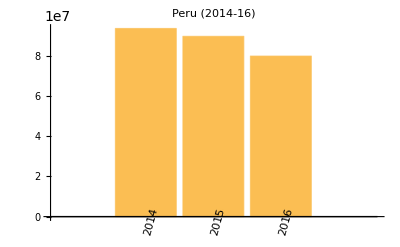

```mathematica
barchartPeru=BarChart[{totalpiechartCountry2014["Peru"],totalpiechartCountry2015["Peru"],totalpiechartCountry2016["Peru"]},PlotLabel->"Peru (2014-16)",ChartLabels->Placed[{"2014","2015","2016"},Below,Rotate[#,Pi/2.4]&]]
```

```mathematica
Export["peru2016.pdf",peru2016]
```

peru2016.pdf

```mathematica
Export["peru2015.pdf",peru2015]
```

peru2015.pdf

```mathematica
Export["peru2014.pdf",peru2014]
```

peru2014.pdf

```mathematica
Export["peru20141516.pdf",barchartPeru]
```

peru20141516.pdf

## Jordan - 2016 - 2015 - 2014

```mathematica
jordan2016
```

-Graphics-

```mathematica
jordan2015
```

-Graphics-

```mathematica
jordan2014
```

-Graphics-

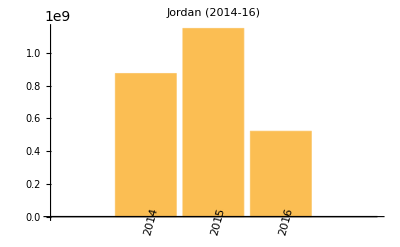

```mathematica
barchartJordan=BarChart[{totalpiechartCountry2014["Jordan"],totalpiechartCountry2015["Jordan"],totalpiechartCountry2016["Jordan"]},PlotLabel->"Jordan (2014-16)",ChartLabels->Placed[{"2014","2015","2016"},Below,Rotate[#,Pi/2.4]&]]
```

```mathematica
Export["jordan2016.pdf",jordan2016]
```

jordan2016.pdf

```mathematica
Export["jordan2015.pdf",jordan2015]
```

jordan2015.pdf

```mathematica
Export["jordan2014.pdf",jordan2014]
```

jordan2014.pdf

```mathematica
Export["jordan20141516.pdf",barchartJordan]
```

jordan20141516.pdf

## Chile - 2016 - 2015 - 2014

```mathematica
chile2016
```

-Graphics-

```mathematica
chile2015
```

-Graphics-

```mathematica
chile2014
```

-Graphics-

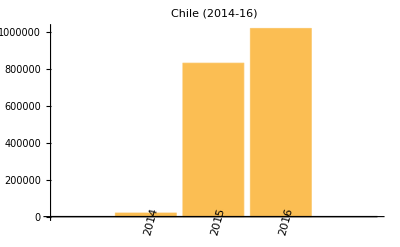

```mathematica
barchartChile=BarChart[{totalpiechartCountry2014["Chile"],totalpiechartCountry2015["Chile"],totalpiechartCountry2016["Chile"]},PlotLabel->"Chile (2014-16)",ChartLabels->Placed[{"2014","2015","2016"},Below,Rotate[#,Pi/2.4]&]]
```

```mathematica
Export["chile2016.pdf",chile2016]
```

chile2016.pdf

```mathematica
Export["chile2015.pdf",chile2015]
```

chile2015.pdf

```mathematica
Export["chile2014.pdf",chile2014]
```

chile2014.pdf

```mathematica
Export["chile20141516.pdf",barchartChile]
```

chile20141516.pdf

## Ethiopia - 2016 - 2015 - 2014

```mathematica
ethiopia2016
```

-Graphics-

```mathematica
ethiopia2015
```

-Graphics-

```mathematica
ethiopia2014
```

-Graphics-

```mathematica
Export["ethiopia2014.pdf",ethiopia2014]
```

ethiopia2014.pdf

```mathematica
Export["ethiopia2015.pdf",ethiopia2015]
```

ethiopia2015.pdf

```mathematica
Export["ethiopia2016.pdf",ethiopia2016]
```

ethiopia2016.pdf

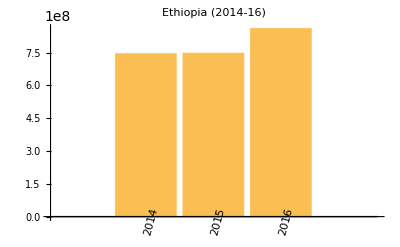

```mathematica
barchartEthiopia=BarChart[{totalpiechartCountry2014["Ethiopia"],totalpiechartCountry2015["Ethiopia"],totalpiechartCountry2016["Ethiopia"]},PlotLabel->"Ethiopia (2014-16)",ChartLabels->Placed[{"2014","2015","2016"},Below,Rotate[#,Pi/2.4]&]]
```